```mathematica
ClearAll["Global`*"]
```

```mathematica
(*eqnP = (w*bPred1*P*C1 +(1-w)* bPred2*P*C2) - μPred*P/.{bPred1->bPred[M],bPred2->bPred[ϕ*M],μPred->μPred[M]}; (*,σPred->σPred[M],kC->kCons[M],Sub->Sub[M]*)
eqnC1 = λ1*(R/(k/2+R))*C1-( σ1*(1-R/k)+μ1+w*b1*P)*C1/.{k->kRes,λ1->λ[M],μ1->μ[M],σ1->σ[M],b1->b[M]};
eqnC2 = λ2*(R/(k/2+R))*C2-( σ2*(1-R/k)+μ2+(1-w)*b2*P)*C2/.{k->kRes,λ2->λ[ϕ*M],μ2->μ[ϕ*M],σ2->σ[ϕ*M],b2->b[ϕ*M]};
eqnR = α*R*(1-R/(k))-( λ1/Y1*(R/(k/2+R)))*C1-( λ2/Y2*(R/(k/2+R)))*C2/.{k->kRes,λ1->λ[M],Y1->Y[M],λ2->λ[ϕ*M],Y2->Y[ϕ*M]};
LVSS = FullSimplify[Solve[{0==eqnP,0==eqnC1,0==eqnC2,0==eqnR},{P,C1,C2,R}]];
*)
```

```mathematica
(*Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/TwoPreySolutions.m"}],LVSS]*)
```

```mathematica
LVSS = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/TwoPreySolutions.m"}]];
```

```mathematica
Length[LVSS]
```

14

```mathematica
(*Internal Fixed Point*)
Psol = P/.LVSS[[13]]
C1sol = C1/.LVSS[[13]]
C2sol=C2/.LVSS[[13]]
Rsol = R/.LVSS[[13]]
(*Boundary Fixed Points*)
PsolC1only = P/.LVSS[[10]];
C1solC1only = C1/.LVSS[[10]];
C2solC1only=C2/.LVSS[[10]];
RsolC1only = R/.LVSS[[10]];

PsolC2only = P/.LVSS[[12]];
C1solC2only = C1/.LVSS[[12]];
C2solC2only=C2/.LVSS[[12]];
RsolC2only = R/.LVSS[[12]];
```

(kRes (-1+w) b[M ϕ] (-σ[M] (2 λ[M] (λ[M ϕ]-2 μ[M ϕ])+λ[M ϕ] (2 μ[M]+3 σ[M]))+λ[M] (2 λ[M]-2 μ[M]+3 σ[M]) σ[M ϕ])+kRes w b[M] (-2 λ[M ϕ]^2 σ[M]+λ[M] σ[M ϕ] (2 μ[M ϕ]+3 σ[M ϕ])+λ[M ϕ] (2 μ[M ϕ] σ[M]+(2 λ[M]-4 μ[M]-3 σ[M]) σ[M ϕ]))+λ[M ϕ] σ[M] √(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2))-λ[M] σ[M ϕ] √(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2)))/(4 kRes ((-1+w) b[M ϕ] λ[M]+w b[M] λ[M ϕ]) ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]))

(Y[M] ((-1+w)^2 b[M ϕ]^2 (4 λ[M ϕ] μPred[M] σ[M]^2-kRes (-1+w) α bPred[M ϕ] Y[M ϕ] (2 (λ[M]-μ[M])^2-(λ[M]-3 μ[M]) σ[M]))+(-1+w) b[M ϕ] (w b[M] (8 λ[M ϕ] μPred[M] σ[M] σ[M ϕ]+kRes (-1+w) α bPred[M ϕ] Y[M ϕ] (λ[M ϕ] (4 μ[M]+σ[M])-μ[M ϕ] (4 μ[M]+3 σ[M])-3 μ[M] σ[M ϕ]+λ[M] (-4 λ[M ϕ]+4 μ[M ϕ]+σ[M ϕ])))+(-1+w) α bPred[M ϕ] Y[M ϕ] (λ[M]-μ[M]) √(kRes^2 ((-1+w)^2 b[M ϕ]^2 (4 λ[M]^2-4 λ[M] (2 μ[M]+σ[M])+(2 μ[M]+3 σ[M])^2)+2 (-1+w) w b[M] b[M ϕ] (4 (λ[M]-μ[M]) (λ[M ϕ]-μ[M ϕ])-2 (λ[M ϕ]-3 μ[M ϕ]) σ[M]+(-2 λ[M]+6 μ[M]+9 σ[M]) σ[M ϕ])+w^2 b[M]^2 (4 λ[M ϕ]^2-4 λ[M ϕ] (2 μ[M ϕ]+σ[M ϕ])+(2 μ[M ϕ]+3 σ[M ϕ])^2))))+w b[M] (w b[M] (4 λ[M ϕ] μPred[M] σ[M ϕ]^2+kRes (-1+w) α bPred[M ϕ] Y[M ϕ] (-2 (λ[M ϕ]-μ[M ϕ])^2+(λ[M ϕ]-3 μ[M ϕ]) σ[M ϕ]))+(-1+w) α bPred[M ϕ] Y[M ϕ] (λ[M ϕ]-μ[M ϕ]) √(kRes^2 ((-1+w)^2 b[M ϕ]^2 (4 λ[M]^2-4 λ[M] (2 μ[M]+σ[M])+(2 μ[M]+3 σ[M])^2)+2 (-1+w) w b[M] b[M ϕ] (4 (λ[M]-μ[M]) (λ[M ϕ]-μ[M ϕ])-2 (λ[M ϕ]-3 μ[M ϕ]) σ[M]+(-2 λ[M]+6 μ[M]+9 σ[M]) σ[M ϕ])+w^2 b[M]^2 (4 λ[M ϕ]^2-4 λ[M ϕ] (2 μ[M ϕ]+σ[M ϕ])+(2 μ[M ϕ]+3 σ[M ϕ])^2))))))/(4 ((-1+w) bPred[M ϕ] Y[M ϕ] λ[M]+w bPred[M] Y[M] λ[M ϕ]) ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ])^2)

(Y[M ϕ] (-4 λ[M] μPred[M] ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ])^2-w α b[M ϕ] bPred[M] Y[M] λ[M] √(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2))+w^2 α b[M ϕ] bPred[M] Y[M] λ[M] √(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2))+w^2 α b[M] bPred[M] Y[M] λ[M ϕ] √(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2))+w α b[M ϕ] bPred[M] Y[M] μ[M] √(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2))-w^2 α b[M ϕ] bPred[M] Y[M] μ[M] √(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2))-w^2 α b[M] bPred[M] Y[M] μ[M ϕ] √(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2))+kRes w α bPred[M] Y[M] (-(-1+w)^2 b[M ϕ]^2 (2 (λ[M]-μ[M])^2-(λ[M]-3 μ[M]) σ[M])+w^2 b[M]^2 (-2 (λ[M ϕ]-μ[M ϕ])^2+(λ[M ϕ]-3 μ[M ϕ]) σ[M ϕ])+(-1+w) w b[M] b[M ϕ] (λ[M ϕ] (4 μ[M]+σ[M])-μ[M ϕ] (4 μ[M]+3 σ[M])-3 μ[M] σ[M ϕ]+λ[M] (-4 λ[M ϕ]+4 μ[M ϕ]+σ[M ϕ])))))/(4 ((-1+w) bPred[M ϕ] Y[M ϕ] λ[M]+w bPred[M] Y[M] λ[M ϕ]) ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ])^2)

1/(4 (-1+w) b[M ϕ] σ[M]+4 w b[M] σ[M ϕ])(-kRes (-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])+kRes w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ])+√(kRes^2 (8 ((-1+w) b[M ϕ] σ[M]+w b[M] σ[M ϕ]) ((-1+w) b[M ϕ] (μ[M]+σ[M])+w b[M] (μ[M ϕ]+σ[M ϕ]))+((-1+w) b[M ϕ] (2 λ[M]-2 μ[M]-σ[M])-w b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ]))^2)))

What are the solutions if the predator is specializing on C1? (w->1)

```mathematica
PsolNoC2= FullSimplify[Psol/.w->1]
C1solNoC2= FullSimplify[C1sol/.w->1]
C2solNoC2= FullSimplify[C2sol/.w->1]
RsolNoC2 = FullSimplify[Rsol/.w->1]
```

1/(4 kRes b[M]^2 λ[M ϕ] σ[M ϕ])((λ[M ϕ] σ[M]-λ[M] σ[M ϕ]) √(kRes^2 b[M]^2 (4 λ[M ϕ]^2-4 λ[M ϕ] (2 μ[M ϕ]+σ[M ϕ])+(2 μ[M ϕ]+3 σ[M ϕ])^2))+kRes b[M] (-2 λ[M ϕ]^2 σ[M]+λ[M] σ[M ϕ] (2 μ[M ϕ]+3 σ[M ϕ])+λ[M ϕ] (2 μ[M ϕ] σ[M]+(2 λ[M]-4 μ[M]-3 σ[M]) σ[M ϕ])))

μPred[M]/bPred[M]

1/(4 b[M] bPred[M] Y[M] λ[M ϕ] σ[M ϕ]^2)Y[M ϕ] (α bPred[M] Y[M] (λ[M ϕ]-μ[M ϕ]) √(kRes^2 b[M]^2 (4 λ[M ϕ]^2-4 λ[M ϕ] (2 μ[M ϕ]+σ[M ϕ])+(2 μ[M ϕ]+3 σ[M ϕ])^2))+b[M] (-4 λ[M] μPred[M] σ[M ϕ]^2+kRes α bPred[M] Y[M] (-2 (λ[M ϕ]-μ[M ϕ])^2+(λ[M ϕ]-3 μ[M ϕ]) σ[M ϕ])))

(kRes b[M] (-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ])+√(kRes^2 b[M]^2 (8 σ[M ϕ] (μ[M ϕ]+σ[M ϕ])+(-2 λ[M ϕ]+2 μ[M ϕ]+σ[M ϕ])^2)))/(4 b[M] σ[M ϕ])

```mathematica
JacobianFullModel=({
{D[eqnP,P],D[eqnP,C1],D[eqnP,C2],D[eqnP,R]},
{D[eqnC1,P],D[eqnC1,C1],D[eqnC1,C2],D[eqnC1,R]},
{D[eqnC2,P],D[eqnC2,C1],D[eqnC2,C2],D[eqnC2,R]},
{D[eqnR,P],D[eqnR,C1],D[eqnR,C2],D[eqnR,R]}})/.{P->Psol,C1->C1sol,C2->C2sol,R->Rsol};
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/carnivoredensities_trimmed.csv"}],"csv"];
ExpPredfitdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ExpPred_fit_table_revreps.csv"}],"csv"];
ExpPredmassdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/ExpPredmass_tablereps.csv"}],"csv"];
LogitMatrixData = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/logit_matrix_meso.csv"}],"csv"];
LogitMatrixMeso = Transpose[{LogitMatrixData[[2;;13,2]],LogitMatrixData[[2;;13,3]],LogitMatrixData[[2;;13,4]]}];
PredMassMeso = {100,51.6,11.9,8.99,3.9,3.249,3.59,2.2,23.2,9.83,5.23,6.949};


kRes=23000;(*grams/m^2 carrying capacity of resource*)

Ed=18200; (*J/g of plant Resource *)
B0=4.7*10^(-2);(*W g^−0.75 for herbivores*)
Em=5774;(*J/gram - energy required to build gram of herbivore*)
a = B0/Em;

(*s=1;*)
Emprime =7000;
aprime =  B0/Emprime;
γ1=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));


τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate of herbivore *)
BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
m0[M_]:=0.097*M^0.92;

(*k=(*10*)23000/2;*)
(*ρ[M_]:=B0*M^(η)/(M*Ed);*)
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)
(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ1+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[M_] := 1/τsig [M];(*starvation mortality rate)*)
η=3/4;
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
B0Pred =(10^0.32)(*kJ/day*)*((0.01157(*Watts*))/(1(*kJ/day*))); (* in (kJ/d) for carnivora from https://doi.org/10.1086/432852 USING LOG10!!!!! *)
EmPred=5774;(*Energy to synthesize a unit of biomass not during starvation J/gram*)

aPred = B0Pred/EmPred;
m0Pred[Mp_]:=0.097*Mp^0.92;
ϵLam = 0.95;
τLamPred[Mp_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0Pred[Mp]/Mp)^(1/4))]*(4*Mp^(1/4))/aPred;
λPred[Mp_]:=(Log[2]/τLamPred[Mp]) (*Fecundity = 2*) 
Bpred[Mp_]:=Integrate[(((1-(1-(m0Pred[Mp]/Mp)^(1/4))*E^(-aPred*t/(4*Mp^(1/4)))))^4)*Mp,{t,0,τLamPred[Mp]}]
PredsperArea[Mp_] :=(0.000862119)*Mp^-0.88; (*Inds/m^2 w/ Mp (grams) From Carbone and Gittleman, Science 2002*)
PredDensity[Mp_] := Mp*PredsperArea[Mp]; (*grams/ind * inds/meter^2 = grams/m^2*)

(*Optimal Predator mass given Prey (M) Mass*)
(*OptPredMass[M_]:=ppmrint*M^ppmrslope;*)

(*A Piecewise function incorporate a) the Cruz/Pires relationship for Prey masses 5-10^4 grams; b) the Hayward relationship fro 10^4-10^7 grams*)
(*breakpoint = 10^4;*)
(*OptPredMass[M_] := Piecewise[{{Exp[3.5]*M,M<breakpoint},{ppmrint*M^ppmrslope,M>=breakpoint}}];*)
```

Calculate the Expected size of a predator given an herbivore consumer of size M

```mathematica
(*Simple Relationship*)
ExpectedPredMassMacro[M_]:=ExpPredint*M^ExpPredslope;
ExpPredslope = (ExpPredfitdata[[3,1]]);
ExpPredint = Exp[(ExpPredfitdata[[2,1]])]*((1/1000)^ExpPredslope)*1000; (*converted from KG to grams*)
(*Integrate over KG mass values, because that is what is used in {alpha,beta,gamma} optimization*)
plink[alpha_,beta_,gamma_,M_,Mp_]:=Exp[alpha+beta*Log[M/Mp]+gamma*Log[M/Mp]^2]/(1+Exp[alpha+beta*Log[M/Mp]+gamma*Log[M/Mp]^2]);
(*Species-Specific Logit Vecs, CONVERTED FROM KG TO GRAMS*)
ExpectedPredMassMeso[logitmatrix_,PredMassVec_,M_]:=(1000*((∑_(j=1)^Length[PredMassVec] plink[logitmatrix[[j,1]],logitmatrix[[j,2]],logitmatrix[[j,3]],Mkg,PredMassVec[[j]]]*PredMassVec[[j]])/(∑_(j=1)^Length[PredMassVec] plink[logitmatrix[[j,1]],logitmatrix[[j,2]],logitmatrix[[j,3]],Mkg,PredMassVec[[j]]])))/.Mkg->(M/1000);


(*Piecewise combination of Meso (Logit) and Macro (Hayward)*)
breakpoint = 10^4;
OptPredMassFunction[M_]:=Piecewise[{
{ExpectedPredMassMeso[LogitMatrixMeso,PredMassMeso,M],M<breakpoint},
{ExpectedPredMassMacro[M],M>=breakpoint}}];


(*Complex Relationship -- doesn't work so well*)
(*plink[alpha_,beta_,gamma_,M_,Mp_]:=Exp[alpha+beta*Log[M/Mp]+gamma*Log[M/Mp]^2]/(1+Exp[alpha+beta*Log[M/Mp]+gamma*Log[M/Mp]^2]);
ExpPredMassGenForm[logitvec_,PredMassMean_,PredMassSD_,M_]:=NIntegrate[plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],M,Mp]*((ⅇ^(-(-PredMassMean+Log[Mp])^2/(2 PredMassSD^2)))/(Mp √(2 π) PredMassSD))*Mp,{Mp,1,10^6}]/NIntegrate[plink[logitvec[[1]],logitvec[[2]],logitvec[[3]],M,Mp]*((ⅇ^(-(-PredMassMean+Log[Mp])^2/(2 PredMassSD^2)))/(Mp √(2 π) PredMassSD)),{Mp,1,10^6}];
PredMassMeso= {5,45,80,250,5000,12500,35000,60000,110000};
alphameso =-1.5;
betameso =-1;
gammameso =-0.12;
logitmeso = {alphameso,betameso,gammameso};
OptPredMass[M_] := Quiet[Evaluate[ExpPredMassGenForm[logitmeso,Log[Mean[PredMassMeso]],(√Log[1/2 ⅇ^(-2 μ) (ⅇ^(2 μ)+√(ⅇ^(4 μ)+4 ⅇ^(2 μ) stdev^2))]/.{μ->Log[Mean[PredMassMeso]],stdev->70000}),M]//Simplify]];*)
```

Create an interpolation function of the Expected Predator Mass relationship bc it is too computationally expensive to use the raw functions!

```mathematica
PredMassTable = Table[{10^i,OptPredMassFunction[10^i]},{i,0,8,0.01}];
OptPredMass=Interpolation[PredMassTable]
```

InterpolatingFunction[…]

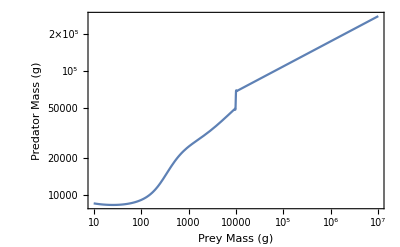

```mathematica
LogLogPlot[OptPredMass[M],{M,10^1,10^7},Frame->True,FrameLabel->{"Prey Mass (g)","Predator Mass (g)"},LabelStyle->Directive[FontSize->16]]
```

```mathematica
(*OptPreypermeter2[Mp_] := 0.1156*OptPreyMass[Mp]^-0.77;
(*Damuth: Average Individuals/m2*)
OptPreygramspermeter2[Mp_] :=OptPreypermeter2[Mp]*OptPreyMass[Mp] ;*)
(*Average Individuals/m2 * average grams/individual*)
(*Percent fat + muscle*)
(*percentconsumable[M_]:=( 0.02*M^1.19 + 0.38*M^1.00)/M;*)
(*Or 1 - percent skeletal*)
massSkeletalgrams[M_]:= 0.0335*M^1.09263;
massFatgrams[M_]:=0.02*M^1.19;
massMusclegrams[M_]:=0.38*M^1.0;
massOthergrams[M_]:=M-(massSkeletalgrams[M]+massFatgrams[M]+massMusclegrams[M]);
(*This is nearly 100% from Prange et al. AmNat 1979*)
(*Energy Density of PREY Joules/gram*)
(*BLUBBER energy content 37670 J/gram SAME AS FAT *)
(*NOTE: THINK CAREFULLY ABOUT THIS *)
FatJperG = 37700;
ProteinJperG = 17900;
MuscleJperG = 0.4*ProteinJperG + 0.6*FatJperG;
(*TissueJperG = ProteinJperG+FatJperG;
PercentFat =(FatJperG/TissueJperG);
PercentProtein =(1- PercentFat);*)
Eprey[M_]:=(1/(M))*(massFatgrams[M]*FatJperG+massMusclegrams[M]*MuscleJperG+massOthergrams[M]*MuscleJperG);
(*Eprey[M_,ϵEprey_] := ((PercentProtein*TissueJperG)+(PercentFat*TissueJperG)+0)*(1+ϵEprey)*percentconsumable[M];*)
(*Joules/gram: 17000 protein + 37000 fat + 0 carb per gram of meat http://www.fao.org/3/y5022e/y5022e04.htm  Modified from Merrill and Watt (1973).*)
(*Results of MAXSIZE are very sensitive to Energy Density of Prey*)
YHerbperRes[M_]:=M*Ed/BLam[M]; (*Grams herb / Grams Resource given the mass of an Herbivore*)
Y[M_]:=YHerbperRes[M];
(*kprey[Mp_]:=OptPreygramspermeter2[Mp]; *)(*PREY carrying capacity grams/m^2*)
Ypred[Mp_,M_] := (Mp*Eprey[M])/Bpred[Mp]; (*Grams of predator per grams of prey*)
PreyDensityTheoreticalMax[M_] :=  Evaluate[YHerbperRes[M]*kRes//Simplify]; 
(*PredatorDensityTheoreticalMax[Mp_,M_]:= Evaluate[Ypred[Mp,M]*YHerbperRes[M]*kRes//Simplify]; *)
PredatorDensityTheoreticalMax[Mp_,M_]:= Evaluate[(*(1/2)**)(Ypred[Mp,M]*YHerbperRes[M]*kRes+Ypred[Mp,ϕ*M]*YHerbperRes[ϕ*M]*kRes)//Simplify]; 
predgrowthrateperconsumer[Mp_,M_] :=λPred[Mp]/PreyDensityTheoreticalMax[M];
(*predatedconsumerdensity[Mp_,M_]:=PredDensity[Mp]/Ypred[Mp,M];*)
(*predatedconsumerdensity[Mp_,M_]:=1/Ypred[Mp,M];*)
(*predrate[Mp_,M_,ϵEprey_] := (λPred[Mp]*PredDensity[Mp])/PredDensityMaxPreyGrowth[Mp,M,ϵEprey](*((1/time)*gpred/m^2)/(gpred/m^2)=1/time*);*)
predmortality = FullSimplify[predgrowthrateperconsumer[Mp,M]*1/Ypred[Mp,M]];
predmortalityfull[Mp_,M_]:=  Evaluate[predmortality//Simplify];
b[M_] :=predmortalityfull[OptPredMass[M],M];

predgrowth =  FullSimplify[predgrowthrateperconsumer[Mp,M]]; (*predatedconsumerdensity without the 1/Yield*)
predgrowthfull[Mp_,M_]:=Evaluate[predgrowth//Simplify];
bPred[M_]:=predgrowthfull[OptPredMass[M],M];
(*bPred[M_]:=λPred[OptPredMass[M]];*)
bPredSub[M_]:=predgrowthfull[OptPredMass[M],M];
(*bPredSub[M_]:=Sub*λPred[OptPredMass[M]];*)



(*Predator starvation*)
σPred[M_]:=(1/τsig [OptPredMass[M]]);
kCons[M_]:=PreyDensityTheoreticalMax[M]; (*Consumer theroetical maximum*)
(*Predator mortality*)
μPred[M_] := (a0*(Exp[a1*a2*OptPredMass[M]^(b1+b2)]-1)*OptPredMass[M]^(b0-b1-b2))/(a1*a2);   (* this is the consumer death rate*)
(*Subsidies could be set as mass dependent or mass-independent*)
(*Sub[M_]:=CsolNoSubsidies;*)
```

```mathematica
(*AverageCsolDensity=Evaluate[NIntegrate[(1/M)*CsolNoSubsidies,{M,10^0,10^7}]];
Sub = ϵ*AverageCsolDensity;*)
```

```mathematica
(*Sub=Evaluate[NIntegrate[(1/M)*CsolNoSubsidies,{M,10^0,10^7}]];*)(*1*)(*0.1*CsolNoSubsidies;*)
```

```mathematica
(*SubDensity=10*Evaluate[NIntegrate[(1/M)*CsolNoSubsidies,{M,10^0,10^7}]]*)
```

Show the inputted PPMR

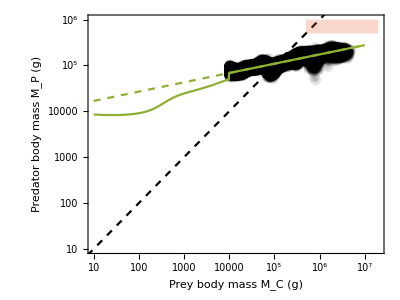

```mathematica
(*nlm = NonlinearModelFit[ExpPredmassdata*1000,nlm1*x^(nlm2),{nlm1,nlm2},x,MaxIterations->1000];
lm =LinearModelFit[Log@(ExpPredmassdata*1000),x,x];
lmparams=lm["BestFitParameters"];
nlmconfint=nlm["ParameterConfidenceIntervals",ConfidenceLevel->0.95];*)
pstyleherb=Graphics[{EdgeForm[{Black,Thickness[0.2],Opacity[0.2]}],Opacity[0.1],FaceForm[Black],Disk[]}];
PPMRPlotNLM = Show[{
ListLogLogPlot[ExpPredmassdata*1000,Frame->True,FrameLabel->{"Prey body mass M_C (g)","Predator body mass M_P (g)"},LabelStyle->Directive[FontSize->16],ImageSize->500,AspectRatio->3/4,PlotMarkers->{pstyleherb,.010},PlotRange->{{10^1,2*10^7},{10^1,10^6}}],
LogLogPlot[M,{M,1,2*10^7},PlotStyle->Directive[Dashed,Black]],
(*LogLogPlot[nlm[x],{x,100,5000}],*)
(*LogLogPlot[nlm[x],{x,100000,3200000},PlotStyle->Directive[Black,Thickness[0.008]]],
LogLogPlot[{nlmconfint[[1,1]]*x^(nlmconfint[[2,1]]),nlmconfint[[1,2]]*x^(nlmconfint[[2,2]])},{x,10^1,3200000},PlotStyle->Transparent,Filling->{1->{2}},FillingStyle->Directive[Green,Opacity[0.25]]],*)
(*ListLogLogPlot[predpreymassdata*1000,PlotStyle->Black],*)
(*LogLogPlot[Exp[lmparams[[1]]]*x^(lmparams[[2]]),{x,10^1,3200000},PlotStyle->ColorData[93,4]],*)
Graphics[{ColorData[97,4],Opacity[0.25],Rectangle[{Log@(5*10^5),Log@(5*10^5)},{Log@(2*10^7),Log@(1*10^6)}]}],
(*Graphics[Text[Style["Megatrophic range",FontSize->16,Black],{Log@(1*10^6),Log@(5*10^(5.5))},Automatic]],*)
(*LogLogPlot[Exp[4]*M,{M,5,1.1*10^5},PlotStyle->ColorData[97,5]] (*Mathias general relationaship*),
LogLogPlot[Exp[3]*M,{M,5,1.1*10^5},PlotStyle->Directive[{ColorData[97,5],Dashed}]] (*Mathias felids relationaship*),*)
LogLogPlot[OptPredMass[M],{M,10^1,10^7},Frame->True,FrameLabel->{"Prey Mass (g)","Predator Mass (g)"},LabelStyle->Directive[FontSize->16],PlotStyle->ColorData[97,3]],
LogLogPlot[ExpectedPredMassMacro[M],{M,10^1,10^7},PlotStyle->Directive[{ColorData[97,3],Dashed}]]
},ImageSize->400,AspectRatio->3/4]
```

Calculate Intersection of Hayward relationship and the 1:1 line
Below this point, predators are LARGER than their prey
Above this point, predators are SMALLER than their prey

```mathematica
N[v0^(1/(1-v1))]/.{v0->ExpPredint,v1->ExpPredslope}
```

111453.

Check Original Model w/o predation... do we get pretty close to the Damuth Data without predation?
1/19/2023 - mass Coordinates for C2 are now converted to M2 units in the plot (where M2 = M1/ϕ)... so instead of a particular feature on the C2 curve relating to the mass of consumer 1, it now relates to the mass of consumer 2. So the x-axis is just ‘Consumer mass’, each C1 and C2 curve relating to M1 and M2, respectively.

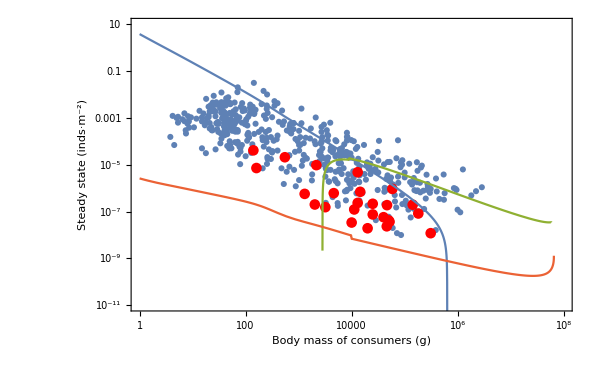

```mathematica
PercentGrowthConsumer1=0.9; (*Percent with which the predator relies on Consumer 1 for food*)
ScaledMassConsumer2 =0.9; (*Proportional size of Consumer 2 with respect to Consumer 1 (focal)*)
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,10}},Frame->True,FrameLabel->{"Body mass of consumers (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*C1sol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]],
LogLogPlot[(((1/(ϕ*M))*C2sol)/.{M->M2/ϕ})/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M2,1,10^8},Frame->True,PlotStyle->ColorData[97,3]],
LogLogPlot[(1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]
}]
```

Detect population thresholds, where the density plummets to zero

```mathematica
(*RealQ[x_]:=Element[x,Reals]===True;*)
RealQ[x_]:=(Im[x]==0)===True; (*THIS WORKS BETTER*)
DetectThresholdLowest[DensitySol_,wvalue_,phivalue_]:=
Module[{Sol = DensitySol},
DiscreteDensityTable = Table[{10^i,(Sol/.{w->wvalue,ϕ->phivalue})/.Mass->10^i},{i,0,7.5,0.05}];
SlopesOfLogs=Transpose[{DiscreteDensityTable[[1;;(Length[DiscreteDensityTable[[All,1]]]-1),1]],Differences[Log[DiscreteDensityTable[[All,2]]]]/Differences[Log[DiscreteDensityTable[[All,1]]]]}];
RealSlopesOfLogsPos =  Flatten[Position[SlopesOfLogs[[All,2]],_?(RealQ[#]&)],1];
RealSlopesOfLogs=SlopesOfLogs[[RealSlopesOfLogsPos]];
(*MinDensity=10^-8;*)
ThresholdDensityPos = Flatten[Position[RealSlopesOfLogs[[All,2]],_?(#==Max[RealSlopesOfLogs[[All,2]]]&)],1];
If[Length[ThresholdDensityPos]>0,
RealSlopesOfLogs[[ThresholdDensityPos[[1]],1]],
Missing[]
]
];
DetectThreshold[DensitySol_,wvalue_,phivalue_]:=
Module[{Sol= DensitySol},
diffSol = Transpose[{Table[10^i,{i,0,7.5-0.01,0.01}],Differences[Table[Abs[(Sol)/.{w->wvalue,ϕ->phivalue}]/.Mass->10^i,{i,0,7.5,0.01}]]*Table[10^i,{i,0,7.5-0.01,0.01}]}];
diffSolMultDiff = Transpose[{Table[10^i,{i,0,7.5-0.02,0.01}],Differences[diffSol[[All,2]]]}];
FirstNegative =Flatten[Position[diffSolMultDiff[[All,2]],_?(#<0&)],1];

(*intvecSol = Intersection[Flatten[Position[diffSol[[All,1]],_?((#>0)&)],1],
Flatten[Position[diffSol[[All,2]],_?(#>0&)],1]];*)
(*intvecSol =Flatten[Position[diffSol[[All,2]],_?(#>0&)],1];*)
(*thresholdpositionC = If[Length[intvecC]==0,Length[diffC],intvecC[[1]]];
thresholdsizeC =  diffC[[thresholdpositionC]][[1]];*)

(*Test to see if there is a threshold at all*)
If[Length[FirstNegative]==0,
Missing[],
thresholdsizeSol = diffSol[[FirstNegative[[1]]]][[1]];
DensityAtMass = (DensitySol/.{w->wvalue,ϕ->phivalue,Mass->thresholdsizeSol*(1-0)});
DensityAtMassLow = (DensitySol/.{w->wvalue,ϕ->phivalue,Mass->thresholdsizeSol*(1-0.1)});
DensityAtMassHigh = (DensitySol/.{w->wvalue,ϕ->phivalue,Mass->thresholdsizeSol*(1+0.1)});
(*Test to make sure it is non-negative and non-imaginary*)
If[(Re[DensityAtMassLow]>0 &&RealQ[DensityAtMassLow])||(Re[DensityAtMassHigh] > 0&&RealQ[DensityAtMassHigh]),
(*Test to make sure it is an extinction threshold, where density -> 0*)
If[Re[DensityAtMass]<Re[DensityAtMassLow]||Re[DensityAtMass]<Re[DensityAtMassHigh],
thresholdsizeSol,
Missing[]
],
Missing[]
]
]
(*thresholdsizeSol*)
];
```

```mathematica
C1solMass = ((1/M)*C1sol)/.M->Mass;
C2solMass = ((1/(ϕ*M))*C2sol)/.{M->Mass/ϕ};
PsolMass = ((1/OptPredMass[M])*Psol)/.{M->Mass};
```

```mathematica
DetectThresholdLowest[C1solMass,PercentGrowthConsumer1,ScaledMassConsumer2]
```

707946.

```mathematica
DetectThreshold[C2solMass,PercentGrowthConsumer1,ScaledMassConsumer2]
```

2818.38

Allow w and ϕ to vary, and calculate:
1) The C1 threshold mass (if it exists)
2) The C2 threshold mass (if it exists)
3) The difference in mass from C2 to C1 where 3 populations co-exist (if it exists)

```mathematica
(*wvalues = Table[i,{i,0.01,0.99,0.01}];
phivalues = Table[i,{i,0.01,0.99,0.01}];*)
```

```mathematica
wvalues = Table[i,{i,0.01,0.99,0.02}];
phivalues = Table[i,{i,0.01,0.99,0.02}];
C1Thresholds = Flatten[ParallelTable[
{wvalues[[i]],phivalues[[j]],DetectThresholdLowest[C1solMass,wvalues[[i]],phivalues[[j]]]},
{i,1,Length[wvalues]},{j,1,Length[phivalues]}],1];
C2Thresholds = Flatten[ParallelTable[
{wvalues[[i]],phivalues[[j]],DetectThresholdLowest[C2solMass,wvalues[[i]],phivalues[[j]]]},
{i,1,Length[wvalues]},{j,1,Length[phivalues]}],1];
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsC1C2overWPhi_HaywardLogit.m"}],{C1Thresholds,C2Thresholds}]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsC1C2overWPhi_HaywardLogit.m

```mathematica
(*C1C2ThresholdData = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsC1C2overWPhi_HaywardLogit.m"}]];
C1Thresholds=C1C2ThresholdData[[1]];
C2Thresholds=C1C2ThresholdData[[2]];*)
```

```mathematica
(*C1C2Thresholds = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsC1C2overWPhi_HaywardLogit.m"}]];
C1Thresholds = C1C2Thresholds[[1]];
C2Thresholds = C1C2Thresholds[[2]];*)
```

```mathematica
MissingPosC1 = Flatten[Position[C1Thresholds[[All,3]],_?(#==Missing[]&)],1];
MissingPointsC1 = Transpose[{C1Thresholds[[MissingPosC1]][[All,1]],C1Thresholds[[MissingPosC1]][[All,2]]}];
MissingPosC2 = Flatten[Position[C2Thresholds[[All,3]],_?(#==Missing[]&)],1];
MissingPointsC2 = Transpose[{C2Thresholds[[MissingPosC2]][[All,1]],C2Thresholds[[MissingPosC2]][[All,2]]}];
```

```mathematica
logTicks[min_,max_]:={#,10^#}&/@FindDivisions[{min,max},5]
```

```mathematica
logTicks[1,7]
```

{{0,1},{2,100},{4,10000},{6,1000000},{8,100000000}}

```mathematica
N[Log10[3*10^7]]
```

7.47712

```mathematica
(*Only way I can think of to force even scales*)
C1Thresholds[[1,3]]=10;
MaxMass = 3.019951720402019*^7;
ThresholdPlot=GraphicsRow[{
Show[{
ListContourPlot[C1Thresholds,FrameLabel->{"Proportional growth from Consumer 1","Proportional size of Consumer 2"},ScalingFunctions->{None,None,"Log"},LabelStyle->Directive[FontSize->16],PlotLegends->BarLegend[{ColorData[{"SandyTerrain","Reverse"}],{Log10[10],Log10[MaxMass]}},Ticks->logTicks[1,Log10[MaxMass]],LegendLabel->"C_1^† thresh."],ColorFunction->ColorData[{"SandyTerrain","Reverse"}],PlotRange->{10,MaxMass},Contours->20,ContourStyle->None],
(*ListPlot[MissingPointsC1],*)
Graphics[{White,Opacity[1],ConcaveHullMesh[MissingPointsC1,0.02,All]}]
},ImageSize->350],
Show[{
ListContourPlot[C2Thresholds,FrameLabel->{"Proportional growth from Consumer 1","Proportional size of Consumer 2"},ScalingFunctions->{None,None,"Log"},LabelStyle->Directive[FontSize->16],PlotLegends->BarLegend[{ColorData[{"SandyTerrain","Reverse"}],{Log10[10],Log10[MaxMass]}},Ticks->logTicks[1,Log10[MaxMass]],LegendLabel->"C_2^† thresh."],ColorFunction->ColorData[{"SandyTerrain","Reverse"}],PlotRange->{10,3.019951720402019*^7},Contours->20,ContourStyle->None],
(*ListPlot[MissingPointsC2],*)
(*Graphics[{White,Opacity[1],ConcaveHullMesh[MissingPointsC2,0.01]}],*)
Graphics[{White,Opacity[1],ConcaveHullMesh[MissingPointsC1,0.02,All]}]
},ImageSize->350]
},ImageSize->1000]
```

-Graphics-

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdsC1C2_w_phi_HaywardLogit.pdf"}],ThresholdPlot]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdsC1C2_w_phi_HaywardLogit.pdf

```mathematica
DiffThreshold = Transpose[{C1Thresholds[[All,1]],C2Thresholds[[All,2]],C1Thresholds[[All,3]]-C2Thresholds[[All,3]]}];
```

```mathematica
Max[DiffThreshold[[Flatten[Position[DiffThreshold[[All,3]],_?(#>0&)],1],3]]]
```

Max[3.01987×10^7,10-Missing,741310.-Missing,977237.-Missing,1.07152×10^6-Missing,1.1749×10^6-Missing,1.31826×10^6-Missing,1.47911×10^6-Missing,1.54882×10^6-Missing,1.99526×10^6-Missing,2.81838×10^6-Missing,2.95121×10^6-Missing,3.98107×10^6-Missing,4.16869×10^6-Missing]

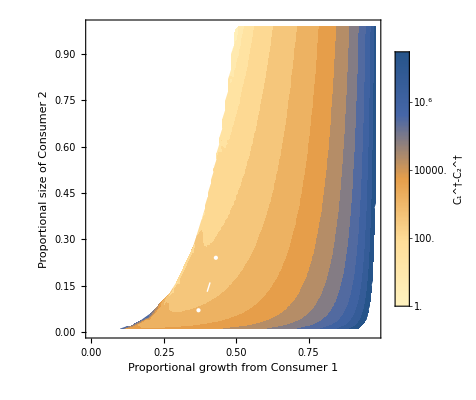

```mathematica
MaxDiff = 3.0198666065981988*^7;
DiffThresholdPlot = Show[{
ListContourPlot[DiffThreshold,FrameLabel->{"Proportional growth from Consumer 1","Proportional size of Consumer 2"},ScalingFunctions->{None,None,"Log"},LabelStyle->Directive[FontSize->16],ColorFunction->ColorData[{"M10DefaultDensityGradient","Reverse"}],PlotLegends->BarLegend[{ColorData[{"M10DefaultDensityGradient","Reverse"}],{Log10[1],Log10[MaxDiff]}},Ticks->logTicks[Log10[1],Log10[MaxDiff]],LegendLabel->"C_1^†-C_2^†"],Contours->20,ContourStyle->None,PlotRange->{1,MaxDiff}],
Graphics[{White,Opacity[1],ConcaveHullMesh[MissingPointsC1,0.02,All]}](*,
Graphics[{ColorData[97,1],Opacity[0.8],ConcaveHullMesh[MissingPointsC2,0.01]}]*)
}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_diffthresholds_w_phi.pdf"}],DiffThresholdPlot]
```

/home/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_diffthresholds_w_phi.pdf

Aside from Thresholds, what is the mass range of feasibility for P, C1, C2?

```mathematica
DetectFeasibilityRange[DensitySol_,wvalue_,phivalue_]:=
Module[{Sol= DensitySol},
MassRange = Table[10^i,{i,0,7.5,0.1}];
DensitiesOverMass =Flatten[Table[Sol/.{w->wvalue,ϕ->phivalue}/.Mass->i,{i,{MassRange}}],1];
(*Find Positive Densities*);
PositiveDensitiesPos = Flatten[Position[DensitiesOverMass,_?(Re[#]>0&&RealQ[#]&)],1];
If[Length[PositiveDensitiesPos]>0,
MaxPosMass = Last[MassRange[[PositiveDensitiesPos]]];
MinPosMass = First[MassRange[[PositiveDensitiesPos]]];
Interval[{MinPosMass,MaxPosMass}],
Interval[]
]
];
```

```mathematica
II=IntervalIntersection[
DetectFeasibilityRange[C1solMass,0.1,0.1],
DetectFeasibilityRange[C2solMass,0.1,0.1],
DetectFeasibilityRange[PsolMass,0.1,0.1]
]
```

Greater::nord: Invalid comparison with 2.06755×10^-8+6.44147×10^-8 ⅈ attempted.

Greater::nord: Invalid comparison with 7.18501×10^-9+4.19184×10^-8 ⅈ attempted.

Greater::nord: Invalid comparison with 3.19789×10^-9+2.91393×10^-8 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Interval[]

```mathematica
DensitiesOverMass =Flatten[Table[C2solMass/.{w->0.1,ϕ->0.1}/.Mass->i,{i,{MassRange}}],1]
```

{3.40962,2.51946,1.86182,1.37595,1.01695,0.751679,0.555657,0.410794,0.303731,0.224597,0.166101,0.122858,0.090886,0.0672452,0.0497625,0.0368321,0.0272673,0.0201909,0.0149548,0.0110795,0.0082109,0.00608698,0.00451407,0.00334891,0.00248556,0.00184564,0.00137118,0.00101925,0.000758122,0.000564273,0.000420301,0.000313317,0.000233772,0.000174593,0.000130534,0.000097708,0.0000732307,0.0000549626,0.000041315,0.0000311084,0.0000234664,0.0000177371,0.000013436,0.0000102021,7.76662×10^-6,5.92922×10^-6,4.54035×10^-6,3.48835×10^-6,2.68973×10^-6,2.08203×10^-6,1.61843×10^-6,1.26381×10^-6,9.91781×10^-7,7.82503×10^-7,6.21017×10^-7,4.96038×10^-7,3.99039×10^-7,3.23569×10^-7,2.64749×10^-7,2.18893×10^-7,1.83237×10^-7,1.55748×10^-7,1.35014×10^-7,1.20248×10^-7,1.11535×10^-7,1.10918×10^-7,1.28214×10^-7,2.59044×10^-7,4.06202×10^-7,2.06755×10^-8+6.44147×10^-8 ⅈ,7.18501×10^-9+4.19184×10^-8 ⅈ,3.19789×10^-9+2.91393×10^-8 ⅈ,1.50677×10^-9+2.10252×10^-8 ⅈ,6.57367×10^-10+1.5516×10^-8 ⅈ,1.86764×10^-10+1.16207×10^-8 ⅈ,-9.35384×10^-11+8.79126×10^-9 ⅈ}

```mathematica
PositiveDensitiesPos = Flatten[Position[DensitiesOverMass,_?(Re[#]>0&&RealQ[#]&)],1]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69}

```mathematica
DensitiesOverMass[[PositiveDensitiesPos]]
```

{3.40962,2.51946,1.86182,1.37595,1.01695,0.751679,0.555657,0.410794,0.303731,0.224597,0.166101,0.122858,0.090886,0.0672452,0.0497625,0.0368321,0.0272673,0.0201909,0.0149548,0.0110795,0.0082109,0.00608698,0.00451407,0.00334891,0.00248556,0.00184564,0.00137118,0.00101925,0.000758122,0.000564273,0.000420301,0.000313317,0.000233772,0.000174593,0.000130534,0.000097708,0.0000732307,0.0000549626,0.000041315,0.0000311084,0.0000234664,0.0000177371,0.000013436,0.0000102021,7.76662×10^-6,5.92922×10^-6,4.54035×10^-6,3.48835×10^-6,2.68973×10^-6,2.08203×10^-6,1.61843×10^-6,1.26381×10^-6,9.91781×10^-7,7.82503×10^-7,6.21017×10^-7,4.96038×10^-7,3.99039×10^-7,3.23569×10^-7,2.64749×10^-7,2.18893×10^-7,1.83237×10^-7,1.55748×10^-7,1.35014×10^-7,1.20248×10^-7,1.11535×10^-7,1.10918×10^-7,1.28214×10^-7,2.59044×10^-7,4.06202×10^-7}

```mathematica
RegionMeasure[II]
```

9952.62

```mathematica
IntervalSizeWPhi = ParallelTable[
C1Interval = DetectFeasibilityRange[C1solMass,wvalues[[i]],phivalues[[j]]];
C2Interval = DetectFeasibilityRange[C2solMass,wvalues[[i]],phivalues[[j]]];
PInterval = DetectFeasibilityRange[PsolMass,wvalues[[i]],phivalues[[j]]];
PC1C2Interval = IntervalIntersection[C1Interval,C2Interval,PInterval];
PC1Interval = IntervalIntersection[C1Interval,PInterval];
PC2Interval = IntervalIntersection[C2Interval,PInterval];
C1C2Interval=IntervalIntersection[C1Interval,C2Interval];
{wvalues[[i]],phivalues[[j]],RegionMeasure[C1C2Interval],RegionMeasure[PC1Interval],RegionMeasure[PC2Interval],RegionMeasure[PC1C2Interval]},
{i,1,Length[wvalues]},{j,1,Length[phivalues]}
];
```

3.16228×10^7

```mathematica
ZeroOverlapPC1C2Pos = Flatten[Position[Flatten[IntervalSizeWPhi,1][[All,6]],_?(#==0&)],1];
ZeroOverlapPC1C2Points = Transpose[{Flatten[IntervalSizeWPhi,1][[ZeroOverlapPC1C2Pos,1]],Flatten[IntervalSizeWPhi,1][[ZeroOverlapPC1C2Pos,2]]}];
```

```mathematica
ZeroOverlapPC1C2Points
```

```mathematica
PlotInterval[IntervalArray_,ColumnID_,Name_]:= Module[{IntervalSizeWPhi=IntervalArray},IntervalSizePC1C2 = Transpose[{Flatten[IntervalSizeWPhi,1][[All,1]],Flatten[IntervalSizeWPhi,1][[All,2]],Flatten[IntervalSizeWPhi,1][[All,ColumnID]]}];
MaxRange=Max[IntervalSizeWPhi[[All,ColumnID]]];
ZeroOverlapPC1C2Pos = Flatten[Position[Flatten[IntervalSizeWPhi,1][[All,ColumnID]],_?(#==0&)],1];
ZeroOverlapPC1C2Points = Transpose[{Flatten[IntervalSizeWPhi,1][[ZeroOverlapPC1C2Pos,1]],Flatten[IntervalSizeWPhi,1][[ZeroOverlapPC1C2Pos,2]]}];
Show[{
ListContourPlot[IntervalSizePC1C2,FrameLabel->{"Proportional growth from Consumer 1","Proportional size of Consumer 2"},ScalingFunctions->{None,None,"Log"},LabelStyle->Directive[FontSize->16],ColorFunction->ColorData[{"M10DefaultDensityGradient","Reverse"}],PlotLegends->BarLegend[{ColorData[{"M10DefaultDensityGradient","Reverse"}],{Log10[1],Log10[MaxRange]}},Ticks->logTicks[Log10[1],Log10[MaxDiff]],LegendLabel->Name],Contours->20,ContourStyle->None,PlotRange->{1,MaxRange}]
(*Graphics[{ColorData[97,1],Opacity[0.8],ConcaveHullMesh[MissingPointsC2,0.01]}]*)
(*ListPlot[ZeroOverlapPC1C2Points]*)
,Graphics[{ColorData[97,4],Opacity[1],ConcaveHullMesh[ZeroOverlapPC1C2Points,0.02,All]}]
,Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[MissingPointsC1,0.02,All]}]
}]
]
```

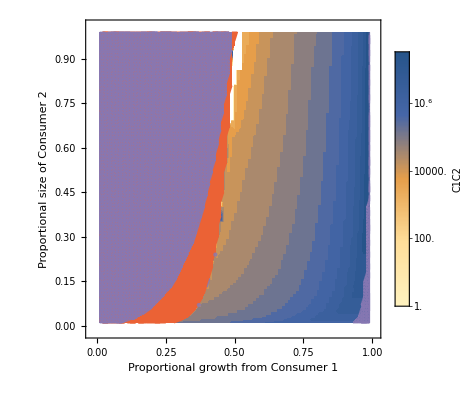

```mathematica
PlotInterval[IntervalSizeWPhi,3,"C1C2"]
```

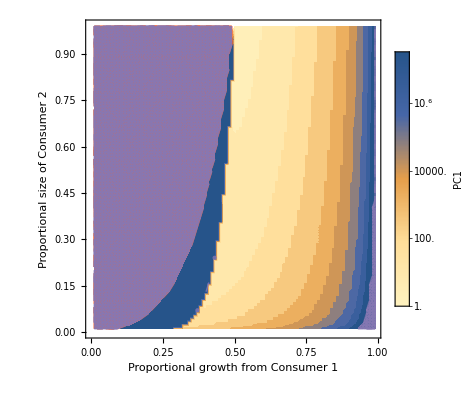

```mathematica
PlotInterval[IntervalSizeWPhi,4,"PC1"]
```

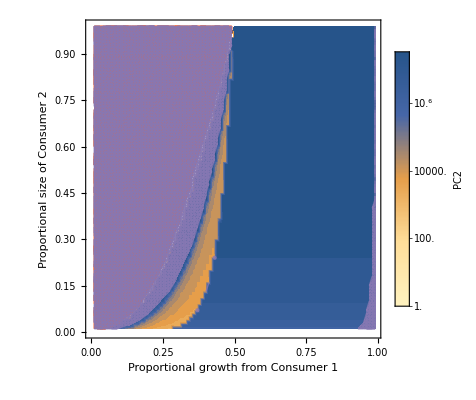

```mathematica
PlotInterval[IntervalSizeWPhi,5,"PC2"]
```

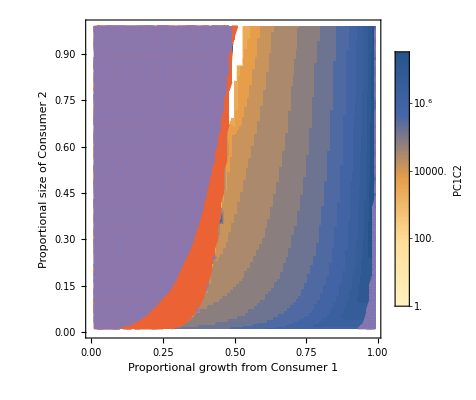

```mathematica
PlotInterval[IntervalSizeWPhi,6,"PC1C2"]
```

Define and plot Regional boundaries for different types of dynamics

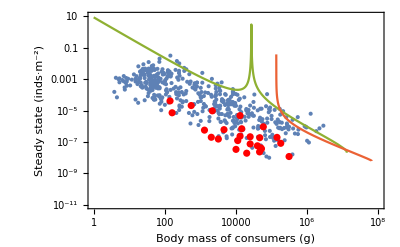

```mathematica
PercentGrowthConsumer1=0.28; (*Percent with which the predator relies on Consumer 1 for food*)
ScaledMassConsumer2 =0.2; (*Proportional size of Consumer 2 with respect to Consumer 1 (focal)*)
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,10}},Frame->True,FrameLabel->{"Body mass of consumers (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*C1sol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]],
LogLogPlot[(((1/(ϕ*M))*C2sol)/.{M->M2/ϕ})/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M2,1,10^8},Frame->True,PlotStyle->ColorData[97,3]],
LogLogPlot[(1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]
}]
```

```mathematica
MaxRange-1000
```

3.16218×10^7

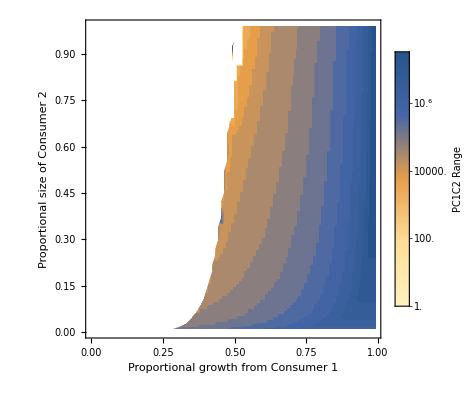

```mathematica
IntervalSizePC1C2 = Transpose[{Flatten[IntervalSizeWPhi,1][[All,1]],Flatten[IntervalSizeWPhi,1][[All,2]],Flatten[IntervalSizeWPhi,1][[All,6]]}];
MaxRange=Max[IntervalSizeWPhi[[All,6]]];
ZeroOverlapPC1C2Pos = Flatten[Position[Flatten[IntervalSizeWPhi,1][[All,6]],_?(#==0&)],1];
ZeroOverlapPC1C2Points = Transpose[{Flatten[IntervalSizeWPhi,1][[ZeroOverlapPC1C2Pos,1]],Flatten[IntervalSizeWPhi,1][[ZeroOverlapPC1C2Pos,2]]}];
Show[{
ListContourPlot[IntervalSizePC1C2,FrameLabel->{"Proportional growth from Consumer 1","Proportional size of Consumer 2"},ScalingFunctions->{None,None,"Log"},LabelStyle->Directive[FontSize->16],ColorFunction->ColorData[{"M10DefaultDensityGradient","Reverse"}],PlotLegends->BarLegend[{ColorData[{"M10DefaultDensityGradient","Reverse"}],{Log10[1],Log10[MaxRange]}},Ticks->logTicks[Log10[1],Log10[MaxDiff]],LegendLabel->"PC1C2 Range"],Contours->20,ContourStyle->None,PlotRange->{1,MaxRange}],(*,
Graphics[{White,Opacity[1],ConcaveHullMesh[MissingPointsC1,0.02,All]}],
Graphics[{ColorData[97,1],Opacity[0.8],ConcaveHullMesh[MissingPointsC2,0.01]}]*)
(*ListPlot[ZeroOverlapPC1C2Points]*)
Graphics[{White,Opacity[1],ConcaveHullMesh[ZeroOverlapPC1C2Points,0.02,All]}]
}]
```

```mathematica
Flatten[IntervalSizeWPhi,1][[1]][[3]]
```

```mathematica
(*Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,10}},Frame->True,FrameLabel->{"Body mass of focal consumer (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*C1sol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]],
LogLogPlot[(1/(ϕ*M))*C2sol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,3]],
LogLogPlot[(1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]
}]*)
```

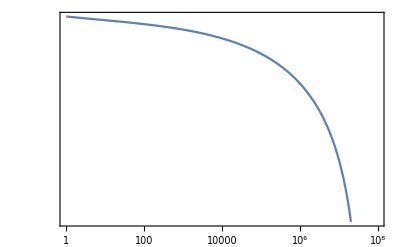

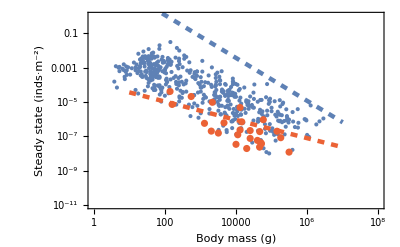

```mathematica
LogLogPlot[Rsol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]]
MaxDensitiesPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->ColorData[97,4]],
LogLogPlot[(1/M)*PreyDensityTheoreticalMax[M]/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/OptPredMass[M])*PredatorDensityTheoreticalMax[OptPredMass[M],M]/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]
}]
```

Given a mass value, phi value, and w value, plot steady states

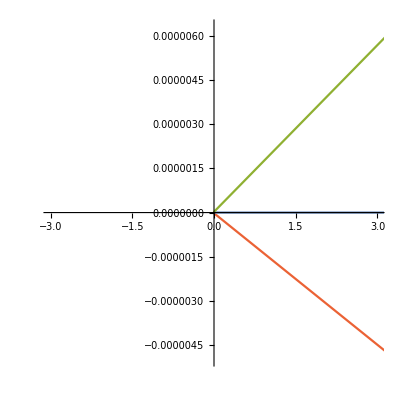

-Graphics-

```mathematica
(*MassValue = 100000;*)
PercentGrowthConsumer1=1; (*Percent with which the predator relies on Consumer 1 for food*)
ScaledMassConsumer2 =0.2; (*Proportional size of Consumer 2 with respect to Consumer 1 (focal)*)
Show[{
ParametricPlot[{(1/M)*C1sol,(1/OptPredMass[M])*Psol}/.{w->PercentGrowthConsumer1,ϕ->1.2},{M,1,10^7},AspectRatio->1,PlotRange->{{-3,3},All},PlotStyle->ColorData[97,4]],
ParametricPlot[{(1/M)*C1sol,(1/OptPredMass[M])*Psol}/.{w->PercentGrowthConsumer1,ϕ->1},{M,1,10^7},AspectRatio->1,PlotRange->All,PlotStyle->ColorData[97,1]],
ParametricPlot[{(1/M)*C1sol,(1/OptPredMass[M])*Psol}/.{w->PercentGrowthConsumer1,ϕ->0.8},{M,1,10^7},AspectRatio->1,PlotRange->All,PlotStyle->ColorData[97,3]]
}]
Show[{
ParametricPlot[{(1/(ϕ*M))*C2sol,(1/OptPredMass[M])*Psol}/.{w->PercentGrowthConsumer1,ϕ->1.2},{M,1,10^7},AspectRatio->1,PlotStyle->ColorData[97,4],ScalingFunctions->{"Log","Log"}],
ParametricPlot[{(1/(ϕ*M))*C2sol,(1/OptPredMass[M])*Psol}/.{w->PercentGrowthConsumer1,ϕ->1},{M,1,10^7},AspectRatio->1PlotStyle->ColorData[97,1],ScalingFunctions->{"Log","Log"}],
ParametricPlot[{(1/(ϕ*M))*C2sol,(1/OptPredMass[M])*Psol}/.{w->PercentGrowthConsumer1,ϕ->0.8},{M,1,10^7},AspectRatio->1,PlotStyle->ColorData[97,3],ScalingFunctions->{"Log","Log"}]
}]
```

```mathematica
v
```

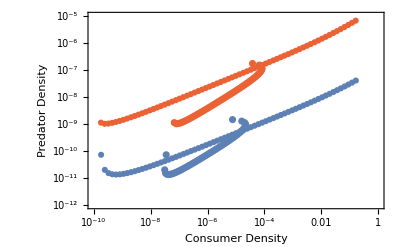

```mathematica
Show[{
ListLogLogPlot[Table[{(1/M)*C1sol,(1/OptPredMass[M])*Psol}/.{M->10^i,w->PercentGrowthConsumer1,ϕ->0.2},{i,1,8,0.1}],PlotStyle->ColorData[97,4],PlotRange->{{10^-10,10^0},{10^-12,10^-5}},Frame->True,FrameLabel->{"Consumer Density","Predator Density"}],
ListLogLogPlot[Table[{(1/(ϕ*M))*C2sol,(1/OptPredMass[M])*Psol}/.{M->10^i,w->PercentGrowthConsumer1,ϕ->0.2},{i,1,8,0.1}],PlotStyle->ColorData[97,4]],
ListLogLogPlot[Table[{(1/(ϕ*M))*C1sol,(1/OptPredMass[M])*Psol}/.{M->10^i,w->PercentGrowthConsumer1,ϕ->0.99},{i,1,8,0.1}],PlotStyle->ColorData[97,1]],
ListLogLogPlot[Table[{(1/(ϕ*M))*C2sol,(1/OptPredMass[M])*Psol}/.{M->10^i,w->PercentGrowthConsumer1,ϕ->0.99},{i,1,8,0.1}],PlotStyle->ColorData[97,1]]
}]
```

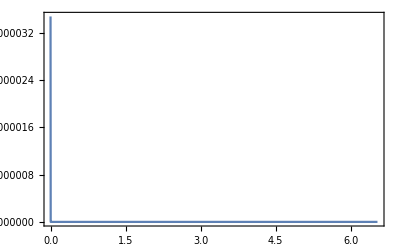

```mathematica
Plot[(1/M)*Psol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1],PlotRange->All]
```

```mathematica
(*detlist = ParallelTable[{10^i,Abs[Det[(JacobianFullModel/.{w->1,Sub->1}/.M->10^i)]]},{i,1,7,0.05}];
thresholdsize = detlist[[Position[detlist,_?(#==Min[detlist]&)][[1]][[1]]]][[1]]
OptPredMass[thresholdsize]
ListLogLogPlot[detlist]*)
```

Now look at results WITH SUBSIDIES

```mathematica
(*Show[{
LogLogPlot[{Table[(1/M)*Sub/.{ϵ->i},{i,0.1,2,0.1}]},{M,1,10^8},PlotStyle->ColorData[97,2],Frame->True],
LogLogPlot[(1/M)*CsolNoSubsidies,{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]]
}]

*)
```

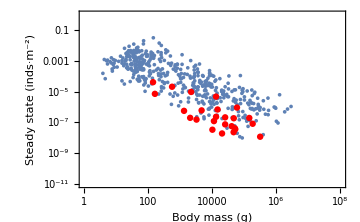

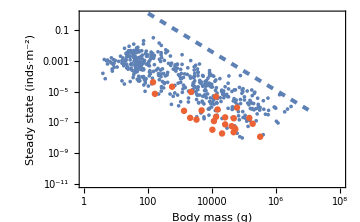

```mathematica
PercentGrowthConsumer=0.1; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidyValue =0.6;
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]],
LogLogPlot[(1/M)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]
}]
MaxDensitiesPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->ColorData[97,4]],
LogLogPlot[(1/M)*PreyDensityTheoreticalMax[M]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/M)*PredatorDensityTheoreticalMax[OptPredMass[M],M]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]
}]
```

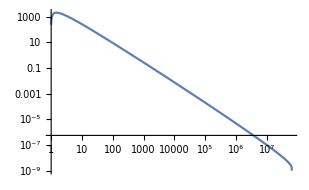

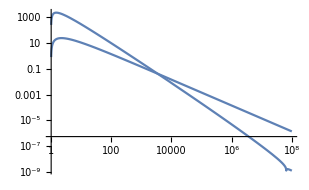

```mathematica
Show[{
LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},PlotRange->All],
LogLogPlot[(1/M)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},PlotRange->All]
}]
Show[{
LogLogPlot[Abs[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}],{M,1,10^8},PlotRange->All],
LogLogPlot[Abs[(1/M)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}],{M,1,10^8}]
}]
```

```mathematica
(*ListLogLogPlot[Transpose[{Table[10^i,{i,0,8-0.01,0.01}],Differences[Table[Abs[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}]/.M->10^i,{i,0,8,0.01}]]*Table[10^i,{i,0,8-0.01,0.01}]}],PlotRange->{{1,10^8},{0.0000000000001,All}}]
ListLogLogPlot[Transpose[{Table[10^i,{i,0,8-0.01,0.01}],Differences[Table[Abs[(1/M)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}]/.M->10^i,{i,0,8,0.01}]]*Table[10^i,{i,0,8-0.01,0.01}]}],PlotRange->{{1,10^8},{0.0000000000001,All}}]*)
```

```mathematica
iterator = 0.1;
diffC = Transpose[{Table[10^i,{i,0,8-0.01,0.01}],Differences[Table[Abs[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}]/.M->10^i,{i,0,8,0.01}]]*Table[10^i,{i,0,8-0.01,0.01}]}];
intvecC = Intersection[Flatten[Position[diffC[[All,1]],_?((#>(10^4*(1+0.1))||#<(10^4*(1-0.1)))&)],1],
Flatten[Position[diffC[[All,2]],_?(#>0&)],1]];
thresholdpositionC = If[Length[intvecC]==0,Length[diffC],intvecC[[1]]];
thresholdsizeC =  diffC[[thresholdpositionC]][[1]]
diffP = Transpose[{Table[10^i,{i,0,8-0.01,0.01}],Differences[Table[Abs[(1/M)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}]/.M->10^i,{i,0,8,0.01}]]*Table[10^i,{i,0,8-0.01,0.01}]}];
intvecP = Intersection[Flatten[Position[diffP[[All,1]],_?((#>(10^4*(1+0.1))||#<(10^4*(1-0.1)))&)],1],
Flatten[Position[diffP[[All,2]],_?(#>0&)],1]];
thresholdpositionP = If[Length[intvecP]==0,Length[diffP],intvecP[[1]]];
thresholdsizeP =  diffP[[thresholdpositionP]][[1]]
```

1.

1.

```mathematica
(*PreySSMin=M/.N[(FindMinimum[{Abs[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}],{M>10001 &&M<10^8}},{M}])][[2]]
PredSSMin=M/.N[(FindMinimum[{Abs[(1/M)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}],{M<10000 }},{M}])][[2]]*)
```

```mathematica
(*(*PercentGrowthConsumer=0.9; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidyValue =0.09;*)
detlist =ParallelTable[{10^i,Abs[Det[(JacobianFullModel/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}/.M->10^i)]]},{i,1,7,0.05}];
thresholdsize = detlist[[Position[detlist,_?(#==Min[detlist]&)][[1]][[1]]]][[1]]
OptPredMass[thresholdsize]
ListLogLogPlot[detlist]*)
```

Evaluate the herbivore and predator body size thresholds across different values of w and Sub

```mathematica
iterator = 0.1;
ThresholdsOverWEpsilon=Flatten[ParallelTable[
(*PreySSMin=M/.N[(FindMinimum[{Abs[(1/M)*Csol/.{w->wvalues,ϵ->epsilonvalues}],{M>10001 &&M<10^8}},{M}])][[2]];
PredSSMin=M/.N[(FindMinimum[{Abs[(1/M)*Psol/.{w->wvalues,ϵ->epsilonvalues}],{M<10000 }},{M}])][[2]];*)
diffC = Transpose[{Table[10^i,{i,0,7.5-0.01,0.01}],Differences[Table[Abs[(1/M)*Csol/.{w->wvalues,ϵ->10^epsilonvalues}]/.M->10^i,{i,0,7.5,0.01}]]*Table[10^i,{i,0,7.5-0.01,0.01}]}];
intvecC = Intersection[Flatten[Position[diffC[[All,1]],_?((#>(10^4*(1+0.1))||#<(10^4*(1-0.1)))&)],1],
Flatten[Position[diffC[[All,2]],_?(#>0&)],1]];
(*thresholdpositionC = If[Length[intvecC]==0,Length[diffC],intvecC[[1]]];
thresholdsizeC =  diffC[[thresholdpositionC]][[1]];*)
thresholdsizeC = If[Length[intvecC]==0,0,diffC[[intvecC[[1]]]][[1]]];
diffP = Transpose[{Table[10^i,{i,0,7.5-0.01,0.01}],Differences[Table[Abs[(1/M)*Psol/.{w->wvalues,ϵ->10^epsilonvalues}]/.M->10^i,{i,0,7.5,0.01}]]*Table[10^i,{i,0,7.5-0.01,0.01}]}];
intvecP = Intersection[Flatten[Position[diffP[[All,1]],_?((#>(10^4*(1+0.1))||#<(10^4*(1-0.1)))&)],1],
Flatten[Position[diffP[[All,2]],_?(#>0&)],1]];
(*thresholdpositionP = If[Length[intvecP]==0,Length[diffP],intvecP[[1]]];*)
(*thresholdsizeP =  diffP[[thresholdpositionP]][[1]];*)
thresholdsizeP = If[Length[intvecP]==0,0,diffP[[intvecP[[1]]]][[1]]];
{wvalues,10^epsilonvalues,thresholdsizeC,thresholdsizeP},
{wvalues,0.05,1,0.05},{epsilonvalues,-3.2,0.3,0.05}],1];
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon.csv"}],ThresholdsOverWEpsilon,"CSV"]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon.csv

```mathematica
ThresholdsOverWEpsilon = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon.csv"}],"CSV"];
```

```mathematica
PreyThresholdMatrix = Transpose[{ThresholdsOverWEpsilon[[All,1]],ThresholdsOverWEpsilon[[All,2]],ThresholdsOverWEpsilon[[All,3]]}];
PredThresholdMatrix = Transpose[{ThresholdsOverWEpsilon[[All,1]],ThresholdsOverWEpsilon[[All,2]],ThresholdsOverWEpsilon[[All,4]]}];
PreySizeGapPos=Flatten[Position[ThresholdsOverWEpsilon[[All,3]],_?(#>1000&&#<10000&)],1];
PredSizeGapPos=Flatten[Position[ThresholdsOverWEpsilon[[All,4]],_?(#>1000&&#<10000&)],1];
PreyTM=PreyThresholdMatrix[[PreySizeGapPos,1;;2]];
PredTM=PreyThresholdMatrix[[PredSizeGapPos,1;;2]];
```

```mathematica
Max[PredThresholdMatrix[[All,3]]]
```

954993.

```mathematica
N[10^(7.5)]
```

3.16228×10^7

```mathematica
ThresholdPlot=GraphicsRow[{
Show[{
ListContourPlot[PreyThresholdMatrix,FrameLabel->{"% Growth from Herbivore (w)","Fraction Subsidy Density (ϵ)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"C Density",LabelStyle->{Italic,FontFamily->"Times New Roman",FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16]],
(*ListLogPlot[PreyThresholdMatrix[[PreySizeGapPos,1;;2]],PlotStyle->Black],*)
Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PreyTM[[All,1]],Log@PreyTM[[All,2]]}]]}]
}],
Show[{
ListContourPlot[PredThresholdMatrix,FrameLabel->{"% Growth from Herbivore (w)","Fraction Subsidy Density (ϵ)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"P Density",LabelStyle->{Italic,FontFamily->"Times New Roman",FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16]],
(*ListLogPlot[PredThresholdMatrix[[PredSizeGapPos,1;;2]],PlotStyle->Black],*)
Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PredTM[[All,1]],Log@PredTM[[All,2]]}]]}]
}]
},ImageSize->800,Spacings->0]
```

-Graphics-

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdsoverwepsilon.pdf"}],ThresholdPlot,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdsoverwepsilon.pdf